```mathematica
SetDirectory[".../Mathematica_Code_Sample/SimDifSpe"]
```

```mathematica
funclist={Exponent, Addilog, CES}
varlist={(tau)}
speclist={GH,CH,LE}
For[i=1,i≤Length[funclist],i++,Print[ToString[funclist⟦i⟧]]]
For[j=1,j≤Length[varlist],j++,Print[ToString[varlist⟦j⟧]]]
For[i=1,i≤Length[funclist],i++,Print[ToString[funclist⟦i⟧]]]
```

{Exponent,Addilog,CES}

{tau}

{GH,CH,LE}

Exponent

Addilog

CES

tau

Exponent

Addilog

CES

```mathematica
For[l=1,l≤Length[speclist],l++,NotebookEvaluate[NotebookOpen[FileNameJoin[{Directory[],"Addilog(tau)_"<>ToString[speclist⟦l⟧]<>".nb"}],Visible->False],InsertResults->False]]
For[l=1,l≤Length[speclist],l++,NotebookEvaluate[NotebookOpen[FileNameJoin[{Directory[],"Exponent(tau)_"<>ToString[speclist⟦l⟧]<>".nb"}],Visible->False],InsertResults->False]]
For[l=1,l≤Length[speclist],l++,NotebookEvaluate[NotebookOpen[FileNameJoin[{Directory[],"CES(tau)_"<>ToString[speclist⟦l⟧]<>".nb"}],Visible->False],InsertResults->False]]
```

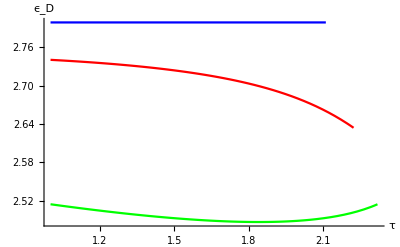
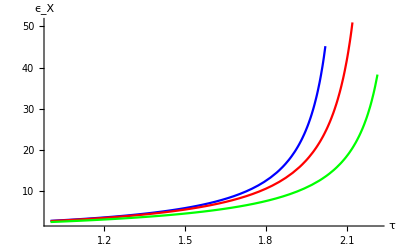
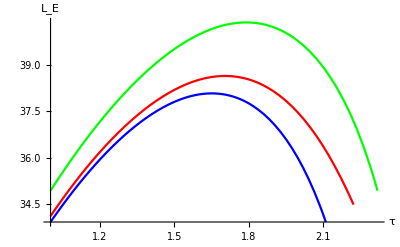
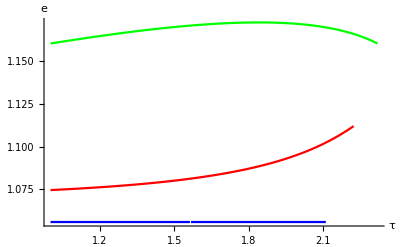
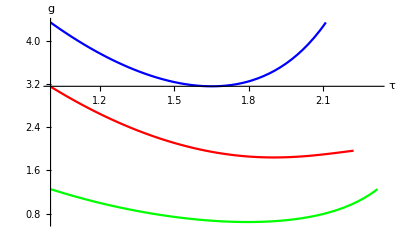
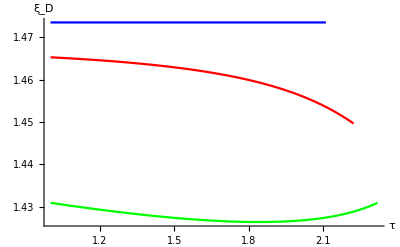
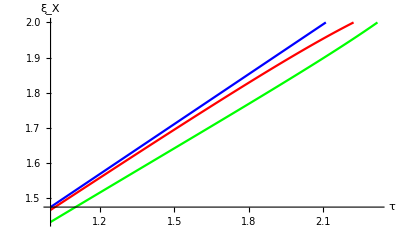
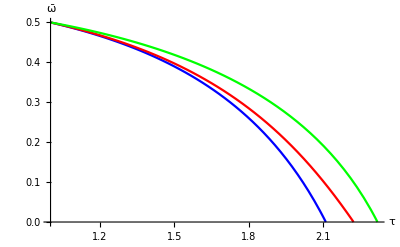

```mathematica
(*The following graphs are created automatically.*)
Table[Show[ToExpression["additauGH"<>ToString[j] ],ToExpression["additauCH"<>ToString[j] ],ToExpression["additauLE"<>ToString[j]],PlotRange->All],{j,15}]
Table[Show[ToExpression["expotauGH"<>ToString[j] ],ToExpression["expotauCH"<>ToString[j] ],ToExpression["expotauLE"<>ToString[j]],PlotRange->All],{j,15}]
Table[Show[ToExpression["CEStauGH"<>ToString[j] ],ToExpression["CEStauCH"<>ToString[j] ],ToExpression["CEStauLE"<>ToString[j]],PlotRange->All],{j,15}]
```